# Lecture 5 - Exercises

Q1: Find the first three roots of the Bessel function J_1(x).

{1.32349×10^-20,10.1735,3.83171}

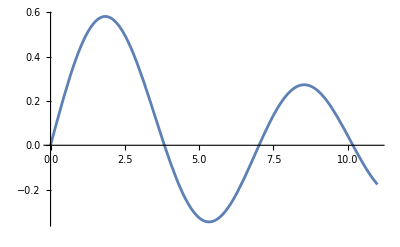

```mathematica
roots=Table[x/. FindRoot[BesselJ[1,x]==0,{x,n}],{n,1,3}]
Plot[BesselJ[1,x],{x,0,11}]
```

Q2 : Integrate the expression f (x) = sin (x) e^-x, and then take its derivative

```mathematica
f[x_]:=sin(x)*e^x
```

```mathematica
t = Integrate[f[x],x]
```

(e^x sin (-1+x Log[e]))/Log[e]^2

```mathematica
Simplify[D[t,x]]
```

e^x sin x

Q4 : Solve the following initial - value problem using both DSolve and NDSolve . Compare your answer by plotting them

```mathematica
ClearAll["Global`*"];
```

```mathematica
DSolve[{y''[x]-x *y[x]==0,y[0]==1, y'[0]==-3^(1/3)*(Gamma(2/3)/Gamma(1/3))},y[x],{x,-10,10}]

NDSolve[{t''[x]-x *t[x]==0,t[0]==1, t'[0]==-3^(1/3)*(Gamma(2/3)/Gamma(1/3))},t[x],{x,-10,10}]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

{{t[x]→InterpolatingFunction[…][x]}}

```mathematica
tnum =(t/.Flatten@%)[x]
```

t[x]

```mathematica
Plot[{y[x],tnum},{x,0,5},AxesLabel->{"x","y[x]"},PlotLegends->{"DSolve","NDSolve"}]
```

-Graphics-